```mathematica
SetDirectory["C:/Users/serha/OneDrive/Masaüstü/MyRepo/master_thesis_MMT003/210421_OR_model_and_other_lines_sliding"];
```

```mathematica
datafull=Import["../data/PLTCM_num.csv",HeaderLines->2];
datafull[[1]]
Dimensions@datafull
```

{3681,8,18000721-03000,327571,4,26,1222.64,4.48514,1.10517,1351.22,19.0359,1802.82,75.8486,120,2.68249,,0,,2,207254,0,678.897,1,1224.67,05.01.18 17:04,1.10509,0,NOOIL,,1,606,421,317,4.48514,1262.69,438.601,1222.64,1772}

{86222,38}

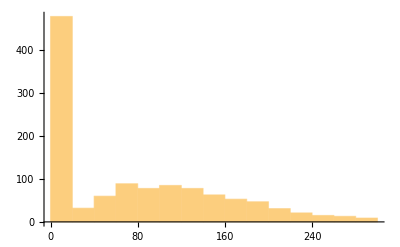

```mathematica
Histogram@Values@Counts@datafull[[All,1]]
```

```mathematica
nullpos=Position[datafull[[All,9]],_?(Head@#==String&)];
datafull=Delete[datafull,nullpos];
```

```mathematica
mostlyzeropos=Join[Position[datafull[[All,12]],_?(#==0&)][[{2,3}]],
Position[datafull[[All,11]],_?(#==0&)][[{2,3}]]];
datafull=Delete[datafull,mostlyzeropos];
```

```mathematica
deletepos=Position[datafull[[All,9]],_?(100<#&)];
datafull=Delete[datafull,deletepos];
```

```mathematica
deletepos3=Position[datafull[[All,7]],_?(4000<#&)];
datafull=Delete[datafull,deletepos3];
```

```mathematica
deletepos2=Position[datafull[[All,7]],_?(100>#&)];
datafull=Delete[datafull,deletepos2];
```

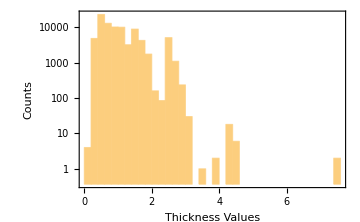
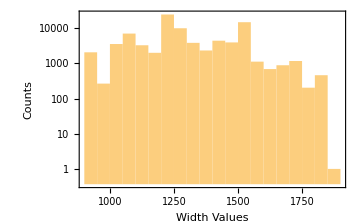

```mathematica
{Histogram[datafull[[All,9]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Thickness Values","Counts"},ImageSize->Medium],Histogram[datafull[[All,7]],ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Width Values","Counts"},ImageSize->Medium]}
```

```mathematica
datafull[[Flatten@Position[datafull[[All,11]],_?Negative],11]]*=(-1);
```

```mathematica
datafull[[Flatten@Position[datafull[[All,12]],_?Negative],12]]*=(-1);
```

```mathematica
density[thick_,width_,length_,weight_]:=N@weight/(thick*width*length);
```

```mathematica
thickvaluesthkpos=datafull[[All,9]];
widthvaluesthkpos=datafull[[All,7]];
lengthvaluesthkpos=datafull[[All,12]];
weightvaluesthkpos=datafull[[All,11]];
densities=Quiet@Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],lengthvaluesthkpos[[i]],weightvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0.,ComplexInfinity->0.};
KeySort@Counts@densities
```

<|0.→23,2.62658×10^-10→1,7.59386×10^-10→1,7.67103×10^-10→1,1.47105×10^-9→1,2.03879×10^-9→1,84800,0.0557443→1,0.0564053→1,0.24686→3,0.287382→2,54.8716→1|>
 |  |  |  |

```mathematica
(* datafull=datafull[[Flatten@Position[densities,_?(0<#<0.0001&)]]]; *)
```

```mathematica
datafull=datafull[[Flatten@Position[densities,_?(6.5*10^(-6)<#<8.5*10^(-6)&)]]];
```

```mathematica
thickvaluesthkpos=datafull[[All,9]];
widthvaluesthkpos=datafull[[All,7]];
lengthvaluesthkpos=datafull[[All,12]];
weightvaluesthkpos=datafull[[All,11]];
densities=Quiet@Table[density[thickvaluesthkpos[[i]],widthvaluesthkpos[[i]],lengthvaluesthkpos[[i]],weightvaluesthkpos[[i]]],{i,Length@thickvaluesthkpos}];
densities=densities/.{Indeterminate->0.,ComplexInfinity->0.};
```

```mathematica
Length@densities
Length@Position[densities,_?(#≤6.5*10^(-6)&)]
Length@Position[densities,_?(8.5*10^(-6)≤#<0.0001&)]
Length@Position[densities,_?(6.5*10^(-6)≤#<8.5*10^(-6)&)]
```

68762

0

0

68762

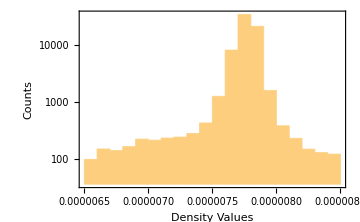

```mathematica
Histogram[densities,ScalingFunctions->"Log",PlotRange->Full,Frame->True,FrameLabel->{"Density Values","Counts"},ImageSize->Medium]
```

```mathematica
datafull=Delete[datafull,Position[datafull[[All,25]],""]];
```

```mathematica
secondscolumn=Table[AbsoluteTime[{datafull[[i,25]],{"Day",".","Month",".","YearShort"," ","Hour",":","Minute"}}],{i,Length@datafull}];
datafull=Join[datafull,Partition[secondscolumn,1],2];
datafullsorted=Sort[datafull,#1[[1]]<#2[[1]]&];
```

Deletion of sequences less than 50

```mathematica
deletepos4=Flatten@Table[Position[datafullsorted[[All,1]],i],{i,Keys@Cases[Normal@Counts@datafullsorted[[All,1]],_?(Values[#]<50&)]}];
datafullsorted=Delete[datafullsorted,Partition[deletepos4,1]];
```

```mathematica
Dimensions@datafullsorted
```

{64026,39}

```mathematica
programids=DeleteDuplicates@datafullsorted[[All,1]];
Length@programids
datafullsortedfinal=Flatten[Table[Sort[Select[datafullsorted,#[[1]]==i&],#1[[39]]<#2[[39]]&],{i,programids}],1];
Dimensions@datafullsortedfinal
```

559

{64026,39}

```mathematica
datafullsortedfinal[[1]]
```

{3609,8,17169021-06000,319652,4,38,1472.14,2.51248,0.468514,689.719,18.2915,3427.1,76.5568,31.2446,2.11253,,0,,2,207148,0,713.984,1,1473.2,29.12.17 18:19,0.468521,0,QUAKEREGL1,,1,610,331,241,2.51248,1535.35,620.727,1472.14,3302,3723560340}

```mathematica
data=Join[Partition[Range@Length@datafullsortedfinal,1],datafullsortedfinal[[All,{1}]],ConstantArray[{0,0,0,0,0,0},Length@datafullsortedfinal],datafullsorted[[All,{7,9,25,39}]],2];
```

```mathematica
data[[1]]
```

{1,3609,0,0,0,0,0,0,1222.64,0.477354,30.12.17 02:14,3723588840}

```mathematica
Dimensions@data
```

{64026,12}

```mathematica
(* Export["pltcm_manipulated_64026.csv",data] *)
```